```mathematica
NS["maxNt3_plots2","C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
(* Plots of maxent distributions for various full-population sizes *)
```

```mathematica
(* stensola *)
which="stensola"; moms=2;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

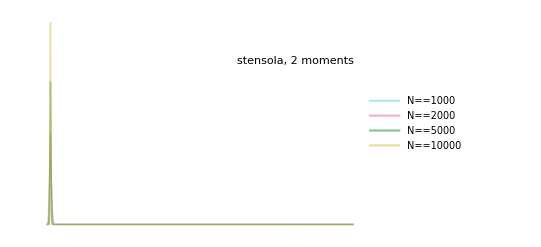

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

stensola2.png

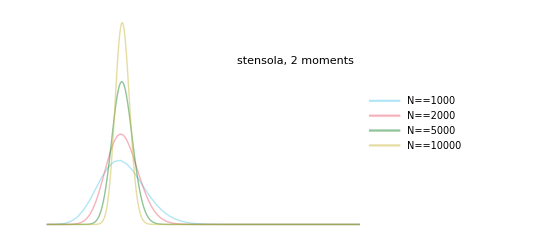

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

stensola2_zoom.png

```mathematica
Log[10,data[[1,Round[0.5*1000],2]]]
```

-191.97572381

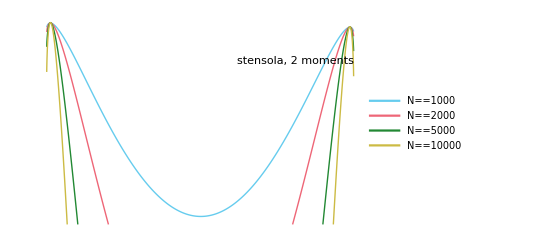

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{All,{10^-200,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

stensola2_log.png

```mathematica
(* stensola  4 moms*)
which="stensola"; moms=4;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

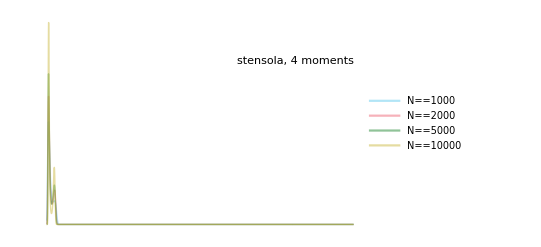

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

stensola4.png

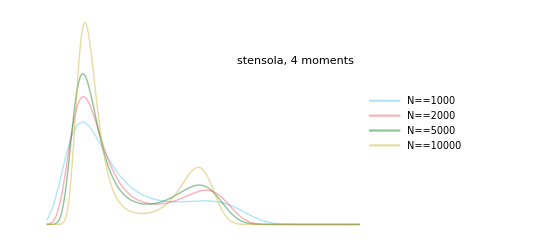

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

stensola4_zoom.png

```mathematica
Log[10,data[[1,Round[0.06*1000],2]]]
```

-36.12752017

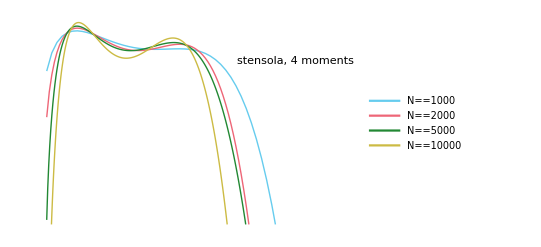

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.06},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

stensola4_log.png

```mathematica
(* riehle 2 moms *)
which="riehle"; moms=2;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

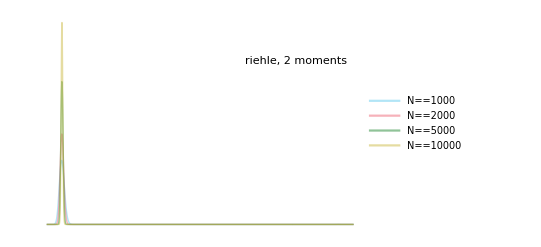

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

riehle2.png

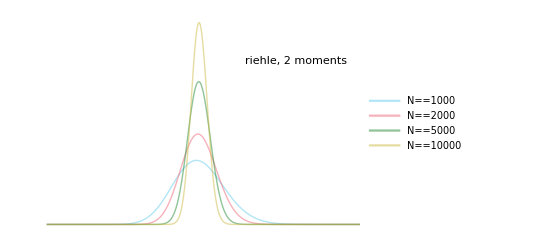

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.1},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

riehle2_zoom.png

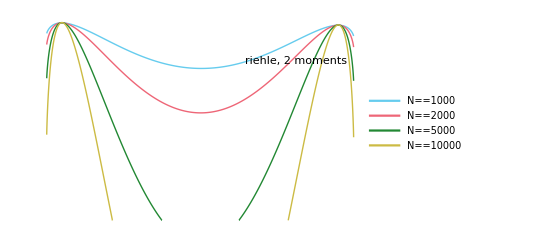

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->Auto,PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

riehle2_log.png

```mathematica
(* riehle 4 moms *)
which="riehle"; moms=4;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

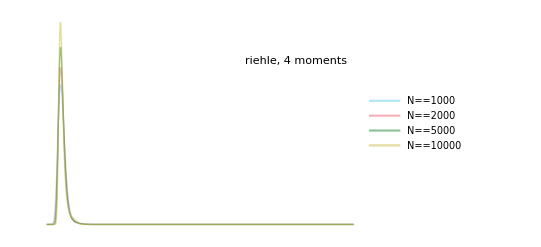

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

riehle4.png

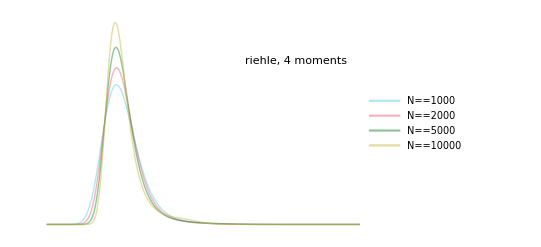

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.2},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

riehle4_zoom.png

```mathematica
Log[10,data[[1,Round[0.25*1000],2]]]
```

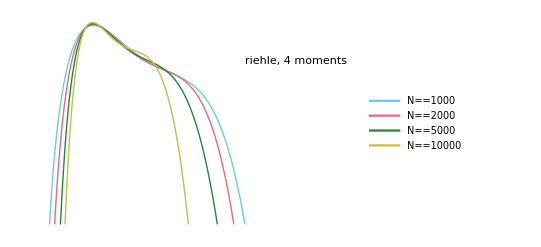

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.3},{10^-9,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

riehle4_log.png

```mathematica
(* ***************************************** *)
(* Plots of marginalizations to different sample sizes *)
(* ***************************************** *)
```

```mathematica
(* stensola 2 moms*)
which="stensola"; moms=2;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

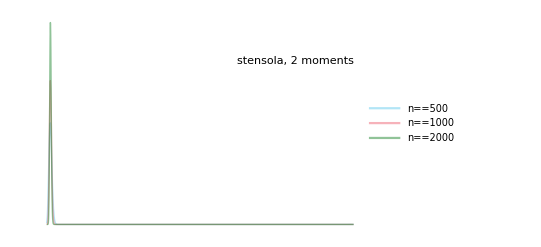

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

stensola2_marginals.png

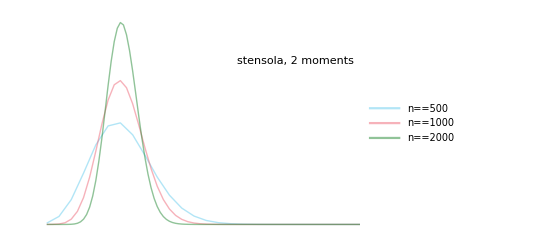

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

stensola2_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

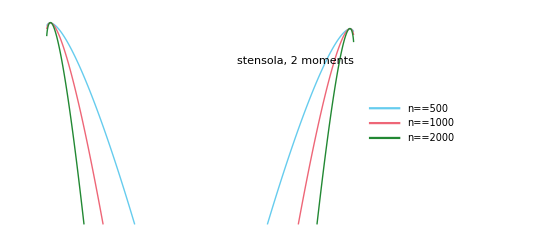

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,All},{10^-140,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

stensola2_marginals_log.png

```mathematica
(* stensola  4 moms*)
which="stensola"; moms=4;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

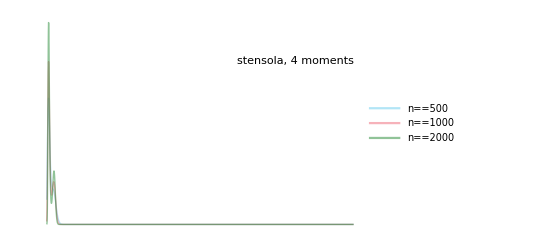

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

stensola4_marginals.png

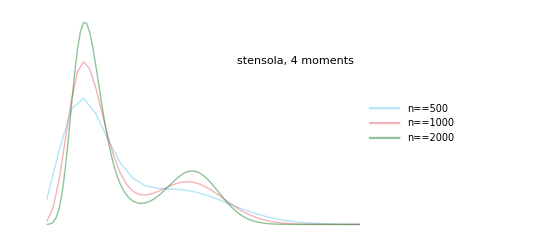

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

stensola4_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

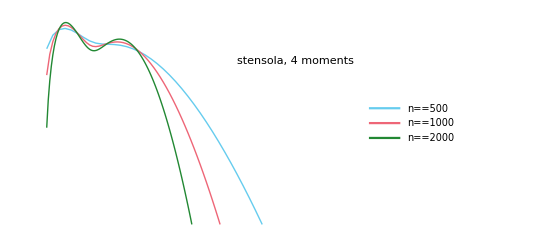

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.1},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

stensola4_marginals_log.png

```mathematica
(* riehle 2 moms *)
which="riehle"; moms=2;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

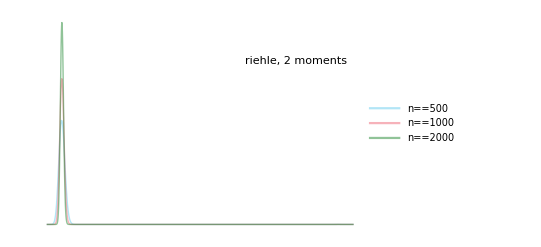

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

riehle2_marginals.png

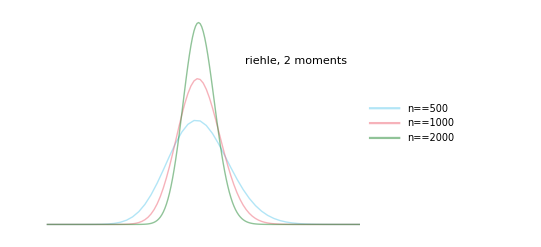

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.1},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

riehle2_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-162.76

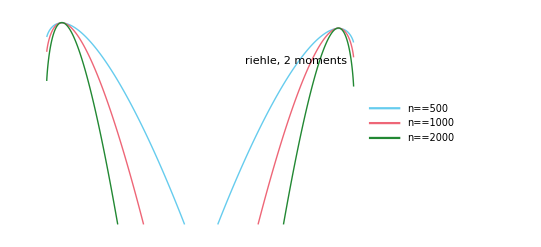

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,All},{10^-140,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

riehle2_marginals_log.png

```mathematica
(* riehle  4 moms*)
which="riehle"; moms=4;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

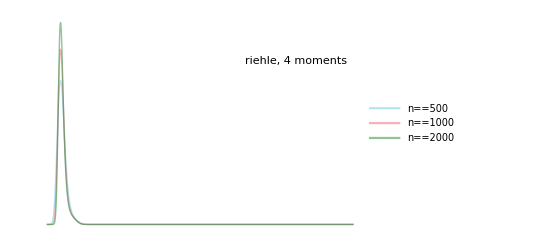

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

riehle4_marginals.png

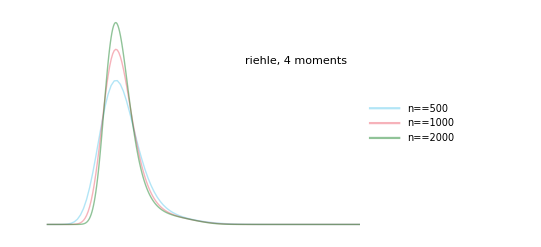

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.2},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

riehle4_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

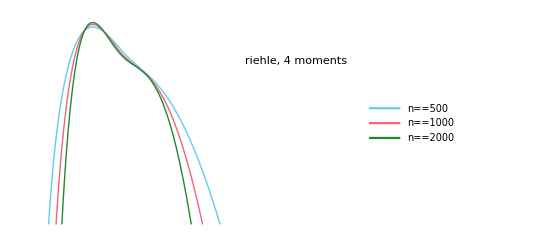

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.3},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

riehle4_marginals_log.png